```mathematica
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)])
(* The following version of Brake[] implements an automatic reaction of the braeaking system if a limit is excieded. The version did not work properly because I may not correctly use the parameters for the break. Adapt it so that it works at the proper time t in the system of equations. *)
```

```mathematica
Brake[t_,τ0_,τ_,βr_]:=Block[{τ01,τ1,β1},
Piecewise[{{τ01={t};τ1={t+2};β1={1.};Fold[Plus,0,Table[Brake1[t-τ01⟦k⟧,τ1⟦k⟧,β1⟦k⟧],{k,1,Length[τ1]}]],Subscript[e, y][t] > 200},{Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]],Subscript[e, y][t] ≤ 200}}]]
```

```mathematica
Brake[t_,τ0_,τ_,βr_]:=
Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
```

```mathematica
(* there was a problem in your definition of Subscript[β, r]. I replaced it by a unique symbol βr. Mathematica hase sometimes problems with indexed variables like your Subscript[β, r]. Good practice is to avoid all indexed variables in subscript notation. *)

τ0 = {1,10,20,50};
τ = {0.6,3,5,5};
β={0,0,0,.0};
βr= Brake[t,τ0 ,τ ,β];
η = √(1.0-βr^2);
```

```mathematica
(* the path must be adjusted on your computer *)

q= Import["1.dat"];
q1 = DeleteCases[Table[If[q[[k,1]] == q[[k+1,1]], null ,q[[k+1]]],{k,1,Length[q]-1}],null];
q2 = Map[({First[#]-0.2945,Last[#]})&,q1];
q3 = Interpolation[q2];
δ= (q3[t]);
```

```mathematica
rules =
{
C1->80000.0,C2->80000.0,C3->80000.0,C4->80000.0,
μ1->1.0,μ2->1.0,μ3->1.0,μ4->1.0,
Fz1->26719.0,Fz2->26719.0,Fz3->21295.0,Fz4->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->5000,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};
```

```mathematica
(* Slip angle *) 
f1[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f1[μ1,Fz1,C1]; Subscript[α, sl2]=f1[μ2,Fz2,C2];
Subscript[α, sl3]=f1[μ3,Fz3,C3]; Subscript[α, sl4]=f1[μ4,Fz4,C4];

f2[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
α1=f2[δ,Subscript[l, f]]; Subscript[α, 2]=f2[δ,Subscript[l, f]];
Subscript[α, 3]=f2[0,-Subscript[l, r]]; Subscript[α, 4]=f2[0,-Subscript[l, r]];
```

```mathematica
(* Tire  Lateral Force *)
f3[C_,α_,μ_,F_,αs_]:=Piecewise[{{- C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3, Abs[α]<αs}, {-η μ F Sign[α], Abs[α]≥αs}}];
Subscript[f, y1]=f3[C1,α1,μ1,Fz1,Subscript[α, sl1]]/.rules; Subscript[f, y2]=f3[C2,Subscript[α, 2],μ2,Fz2,Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f3[C3,Subscript[α, 3],μ3,Fz3,Subscript[α, sl3]]/.rules; Subscript[f, y4]=f3[C4,Subscript[α, 4],μ4,Fz4,Subscript[α, sl4]]/.rules;
```

```mathematica
(* Tire  Longitudinal Force *) 
f4[μ_,F_]:=βr μ F/.rules;
Subscript[f, x1]=f4[μ1,Fz1]/.rules; Subscript[f, x2]=f4[μ2,Fz2]/.rules;
Subscript[f, x3]=f4[μ3,Fz3]/.rules; Subscript[f, x4]=f4[μ4,Fz4]/.rules;
```

```mathematica
(* Long. and Lat. Tot. Forces *)
Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ];
Subscript[F, x3] =Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]; Subscript[F, x4] =Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ];
Subscript[F, y3] =Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]; Subscript[F, y4] =Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0];
```

```mathematica
(*phi = (0) + (Subscript[Ce, 0]*x[t]) +(1/2 Subscript[Ce, 1]*(x[t])^2)
u = (0) + phi*x[t] + (1/2 Subscript[Ce, 0]*(x[t])^2) + (1/6 Subscript[Ce, 1]*(x[t])^3);*)
u[t_] :=  0.0001 t^2+0.5;
(* Equations of Motion *)
Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4];
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4];
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4]);
Eq4 = Subscript[e, ψ]'[t]==( ψ'[t]-u''[t]);
Eq5 = Subscript[e, y]'[t]==(*ψ'[t]-0.0002 t*)y'[t] Cos[Subscript[e, ψ][t]] + x'[t]Sin[Subscript[e, ψ][t]];
```

```mathematica
motionEq ={Eq1,Eq2,Eq3,Eq4,Eq5}/.rules;
time =70;
initCond={x[0]==0.1,x'[0]==10,y[0]==0.0,y'[0]==0.00,ψ[0]==0.00,ψ'[0]==0, Subscript[e, ψ][0] == 00.05, Subscript[e, y][0] == -1};
solution=NDSolve[Flatten[{motionEq/.rules,initCond}],{x,y,ψ,Subscript[e, ψ],Subscript[e, y]},{t,0,time}];
```

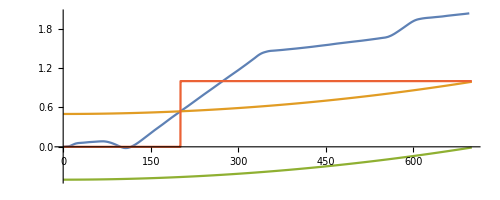

```mathematica
scale =10;
P1 = ParametricPlot[{{x[t],y[t]}/.solution,{scale *t,u[t]},{scale *t, u[t]-1},{scale *t,FlagY/.solution}(*{10t, Subscript[e, y][t]/.solution}{t,Sqrt[(x[t])^2+(y[t])^2]/.solution}*)},{t,0,time},AspectRatio->Full,PlotRange->All]
```

```mathematica
FlagY =Piecewise[{{0, u[t]>y[t] > u[t]-1}, {1, True}}];
Subscript[Flag, ey] =Piecewise[{{1, Subscript[e, y][t] > 200}, {0, Subscript[e, y][t]≤  200}}];
Subscript[Flag, slip1] =Piecewise[{{0, 0.07>α1 > -0.07}, {1, True}}];
Subscript[Flag, slip2] =Piecewise[{{0, 0.07>Subscript[α, 2] > -0.07}, {1, True}}];
Subscript[Flag, slip3] =Piecewise[{{0, 0.07>Subscript[α, 3] > -0.07}, {1, True}}];
Subscript[Flag, slip4]=Piecewise[{{0, 0.07>Subscript[α, 4] > -0.07}, {1, True}}];
```

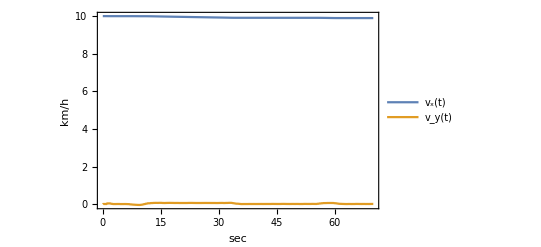

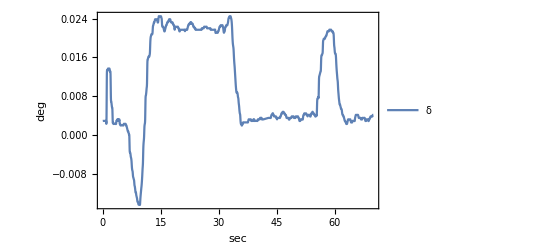

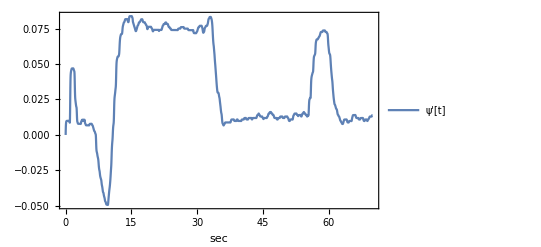

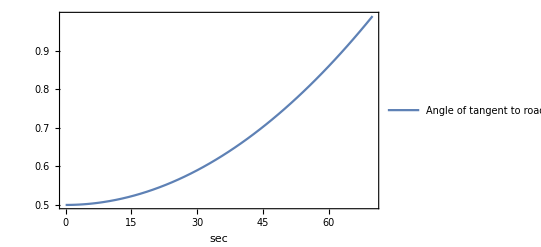

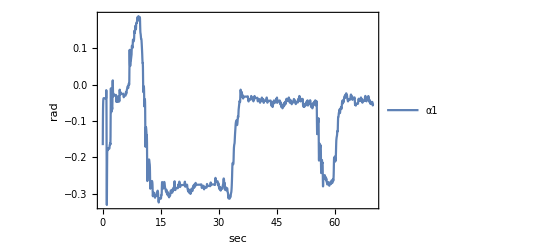

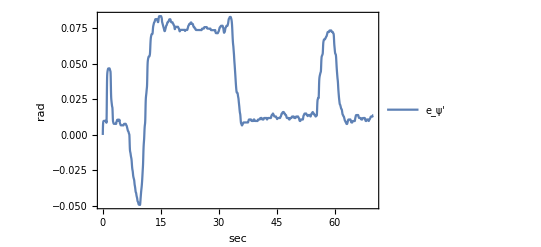

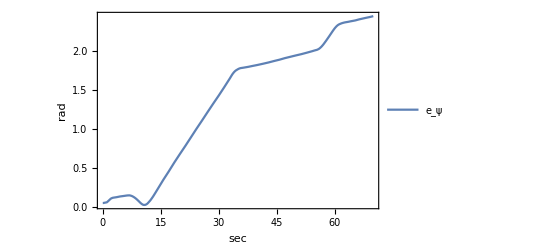

```mathematica
f5[x_,y_,l2_,s1_,s2_]:=Plot[Evaluate[{x,y}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,l2},PlotLegends->{s1,s2},PlotRange->All] ;
f5[x[t],y[t],m,x[t],"y(t)"];
f5[x'[t],y'[t],"km/h","v_x(t)","v_y(t)"]
f5[x''[t],y''[t],"m/s^2","a_x(t)","a_y(t)"];
f5[δ,,"deg","δ",""]
f5[ψ'[t],,"","ψ'[t]",""]
f5[u[t],,"","Angle of tangent to road centerline",""]
Plot1 = ParametricPlot[{{x[t],y[t]}/.solution},{t,0,time},PlotRange-> All,AspectRatio->Full];
Plot2 = ParametricPlot[{{u[t]}},{t,0,time},PlotRange-> All];
Show[{Plot1,Plot2}, PlotRange-> All];
f5[α1*180/π,,"rad","α1",""]
f5[Subscript[e, ψ]'[t]/.solution,,"rad","e_ψ'",""]
f5[Subscript[e, ψ][t]/.solution,,"rad","e_ψ",""]

f5[Subscript[Flag, ey],,"-","Flag_ey",""];
f5[u[t],,"","psid",""];
Plot[Evaluate[{Subscript[Flag, slip1],Subscript[Flag, slip2],Subscript[Flag, slip3],Subscript[Flag, slip4]}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,""},PlotLegends->{"Flag_slip1","Flag_slip2","Flag_slip3","Flag_slip4"},PlotRange->All] ;

(* The upper parabola is the left boundary of the road. The mid parabola is the center of the road. The bottom parabola is the lower bound of the road. There isa flag FlagY tetecting the crossing of the mid of the road. Your flag Subscript[Flag, ey] detects a value of ey[t]. The road is represented using time as parameter. This needs the knowledge of the maximal value of the elongation x as a function of t (here about 700). To match the scales there must be a reduction of x by a factor 10 or an amplification of the x-coordinate of the road by 10 which is used here. The y coordinate of the road uses a scaled version of your curve using C1 and C0 *)
```

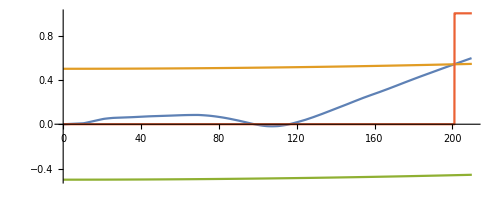

```mathematica
scale =10;
P1 = ParametricPlot[{{x[t],y[t]}/.solution,{scale *t,u[t]},{scale *t, u[t]-1},{scale *t,FlagY/.solution}(*{10t, Subscript[e, y][t]/.solution}{t,Sqrt[(x[t])^2+(y[t])^2]/.solution}*)},{t,0,21},AspectRatio->Full,PlotRange->All]
```

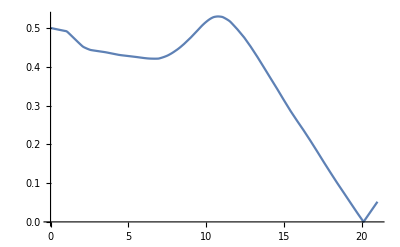

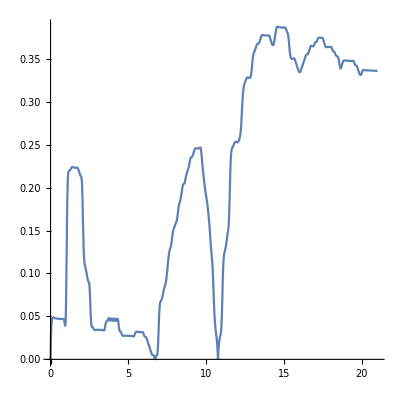

```mathematica
dx = 0;
dy = y[t] - u[t];
dc = {dx,dy};
ce = Sqrt[dc.dc];
Plot[ce/.solution,{t,0,21}]
road= {11,D[u[t],t]};
vel = {x'[t],y'[t]};
k = (road.vel)/(Norm[road]*Norm[vel]);
Plot[ArcCos[k]*180/π/.solution,{t,0,21},AspectRatio->1,PlotRange->All]
```

## Road Model in the Simulation

The idea is to estimate the extension of the motion in x and y direction. So we estimate the maximal extension of the road as (x_min,x_max)×(y_min,y_max) where the extremal values determine the range of a rectangle. Within this range we define the road and the ideal line as an interpolation polynomial as follows. x_min and y_min can be choosen in the origin without any restrictions. If we like to generate a 2^nd order polynomial for the ideal line we need 3 interpolation points which one of them is the origin

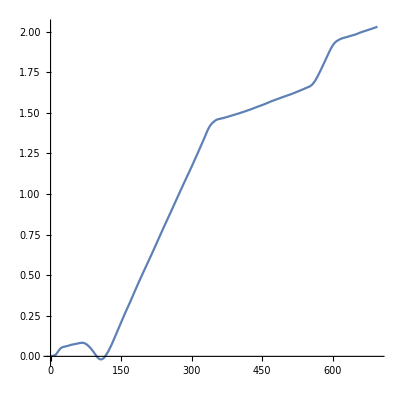

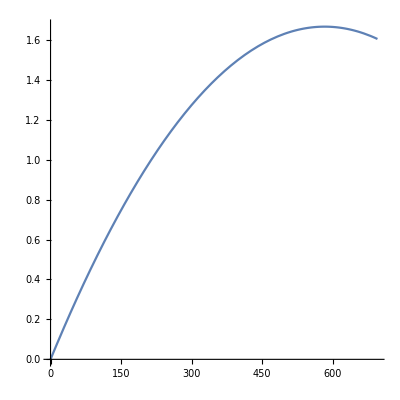

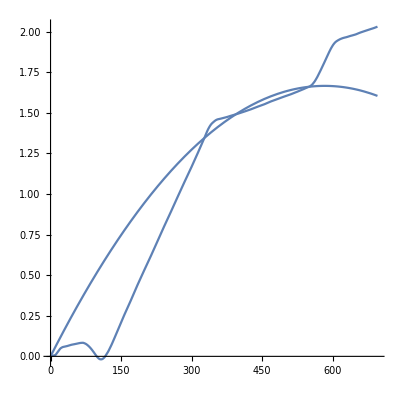

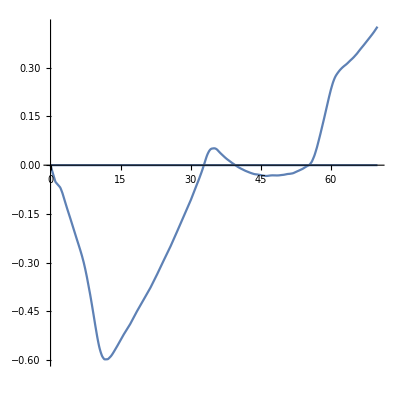

```mathematica
points={{0,0},{700/2,35},{700,40}};
pl1=InterpolatingPolynomial[points,x]/25//Expand;
x1 = ParametricPlot[{x[t],y[t]}/.solution,{t,0,time},AspectRatio->1]
x2 = ParametricPlot[{x[t],pl1/.x-> x[t]}/.solution,{t,0,time},AspectRatio->1]
Show[x1,x2]
ΔxVec={0,-(pl1/.x->x[t])+y[t]};
lineElement=ΔxVec;
x3 = Plot[lineElement/.solution,{t,0,time},AspectRatio->1,PlotRange->Full]
```

```mathematica
tangentVec={1,D[pl1,x]}/.x->x[t]
```

{1,1/175-(3 x[t])/306250}

The velocity is derived from the trajectory of the car as

```mathematica
velocity={x'[t],y'[t]}
```

{x'[t],y'[t]}

The allignement along the ideal track is found by the relation |cos(θ)|=1 which is equivalent to 1=|(t⃗.v⃗)/(|t⃗| |v⃗|)| which is implemented next as difference

```mathematica
ori =  (velocity.tangentVec)/(Norm[velocity] Norm[tangentVec]);
allignment=1-Abs[(velocity.tangentVec)/(Norm[velocity] Norm[tangentVec])];
```

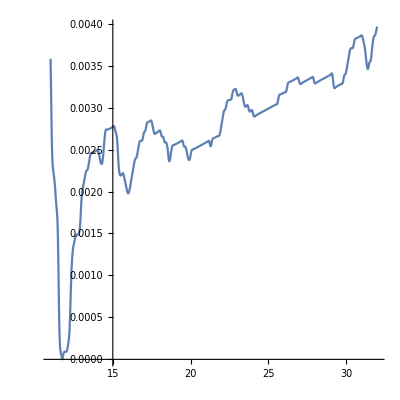

```mathematica
Plot[ArcCos[ori]/.solution,{t,11,32},AspectRatio->1,PlotRange->Full]
```

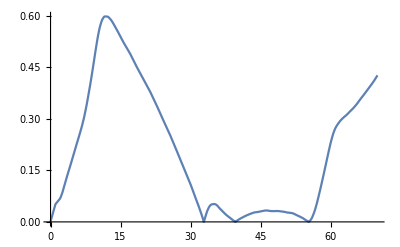

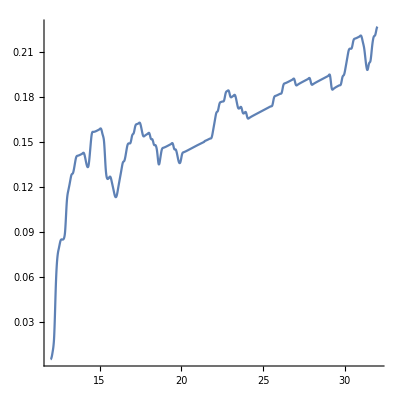

```mathematica
dx = 0;
dy = y[t] - pl1/.x->x[t];
dc = {dx,dy};
ce = Sqrt[dc.dc];
Plot[ce/.solution,{t,0,time}]
road= {1,D[pl1,x]/.x->x[t]};
vel = {x'[t],y'[t]};
k = (road.vel)/(Norm[road]*Norm[vel]);
Plot[ArcCos[k]*180/π/.solution,{t,12,32},AspectRatio->1,PlotRange->All]
```

Finally we need the reference velocity lets call it v_Max which we compare with the current velocity v of the car

```mathematica
ΔVelocity=vMax-Norm[{x'[t],y'[t]}]
```

vMax-√(Abs[x'[t]]^2+Abs[y'[t]]^2)

The cost function can now be written as

```mathematica
kostFunction=α lineElement^2/.{α->1/3}
```

1/3 Abs[x[t]/175-(3 x[t]^2)/612500-y[t]]^2

with α, β, and γ as weights of the function. This implementation should be completely independent of the scaling of the previously used parametric representation of the road.

## How to use the CostFunction

First define the cost function generating the results and using the unspecified parameters in the following example a. I solve a differential equation on a fixed time domain and like to find the value for the parameter a which minimizes my result with respect to a given value for a; e.g. a=2.

This function defines the partial costfunction

```mathematica
f[a_?NumericQ]:=Block[{solution,x,y,ψ,δ},
solution=Flatten[NDSolve[{motionEq,initCond},δ,{x,0,700}]];
vv=(kostFunction=α lineElement^2/.{α->1/3})
]
```

If I use the function with a symbolic argument nothing happens. The definition assumes that a is numeric which is important in the optimization

```mathematica
f[a]
```

f[a]

The cost function I’m interest in is (2-f(a))^2. The following table shows that ther is a minimal value.

```mathematica
Table[(-f[a])^2/.solution,{a,0,5,.1}]
```

NDSolve::ivhead: The independent variable x appears in the head of the expression x[0]. The independent variables should always be arguments.

General::stop: Further output of NDSolve :: ivhead will be suppressed during this calculation.

{{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4}}

The graph represents the same fact

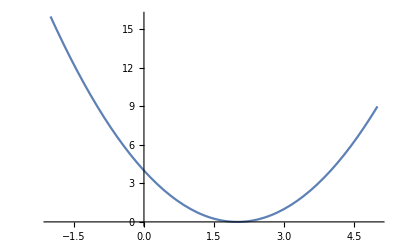

```mathematica
Plot[(2-f[a])^2,{a,-2,5}]
```

Now using FindMinimum allows me to get the minimal value for a which is near by the assumed value

```mathematica
min=FindMinimum[(2-f[a])^2,a]
```

{4.93038×10^-32,{a→2.00014}}

With the optimal solution given by

```mathematica
solution=Flatten[NDSolve[{D[y[x], x]==-y[x]+a/.Last[min],y[0]==-1},y,{x,0,10}]]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

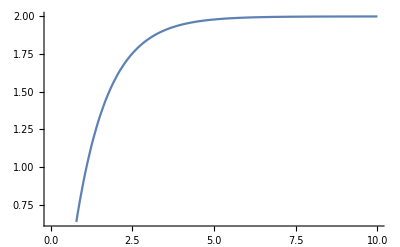

```mathematica
Plot[y[x]/.solution,{x,0,10}]
```